# Creating movies and animations

## Simple animations

Consider the simple function : g(t)=Asin(ω t)

```mathematica
g[l_,A_,ω_]=A*Sin[ω*l]
```

A Sin[l ω]

```mathematica
AExample=3;
ωExample=π;
```

#### Simple plot

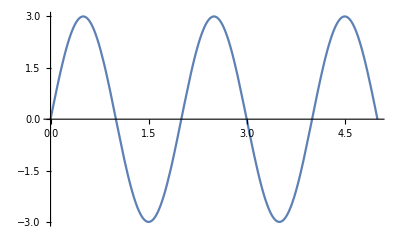

```mathematica
Plot[g[t,AExample,ωExample],{t,0,5}]
```

#### Change parameters dynamically

```mathematica
Manipulate[m*x+3,{m,2,4}]
```

#### Plot with manipulate

```mathematica
Manipulate[Plot[g[t,AExample,ω],{t,0,5}],{ω,1,5}]
```

#### Manipulating more than 1 parameters

```mathematica
Manipulate[Plot[g[t,A,ω],{t,0,5},PlotRange->{-4,4}
,PlotStyle->{Cyan,Dashed,Thickness[0.02]}],{ω,1,5},{A,2,4}]
```